```mathematica
f[a_, b_, ε_,x_,y_] = a*x^2 + b*y^2 + ε*x^4 - 1;
ellplus[a_, b_, ε_,x_] = (√(1-a x^2-x^4 ε))/(√b);
ellminus [a_, b_, ε_,x_]= -(√(1-a x^2-x^4 ε))/(√b);
gradf[a_, b_, ε_,x_,y_] = Grad[f[a,b,ε,x,y],{x,y}];
```

```mathematica
nextCoord[a_, b_, startθ_, startα_, ε_,n_] :=
Module[{start, s, startx, starty, startt,endx, endy ,angle,list, ss, xx, yy, u, slope, v, ϕ, plot,coord,gr1},
start = NSolve[{f[a, b, ε,x,y] == 0,x == t*Cos[startθ],y ==t*Sin[startθ],t≥ 0},{x,y,t},Reals];
s={x,y,t}/.start;
startx = s[[1,1]];
starty = s[[1,2]];
startt = s[[1,3]];
coord = {{startx,starty}};
angle = startα;
j = 1;
list = {};(* stores position angles and trajectory angles*)
While[j ≤ n,
ss=NSolve[{f[a, b, ε,x,y] == 0,x ==startx + t*Cos[angle],y ==starty + t*Sin[angle],t≥ 0},{x,y,t},Reals];
xx= ss[[All,1,2]];
yy= ss[[All,2,2]];
(*Update for next iteration of while loop*)
startx = If[startx ≤  xx[[1]]+0.0000001 && startx ≥   xx[[1]]-0.0000001 ,xx[[2]],xx[[1]]];
starty = If[starty ≤  yy[[1]]+0.0000001 && starty ≥   yy[[1]]-0.0000001,yy[[2]],yy[[1]]];
endx = If[startx ≤  xx[[1]]+0.0000001 && startx ≥   xx[[1]]-0.0000001 ,xx[[2]],xx[[1]]];
endy = If[starty ≤  yy[[1]]+0.0000001 && starty ≥   yy[[1]]-0.0000001,yy[[2]],yy[[1]]];
coord = Append[coord,{startx,starty}];
u = {endx - startx,endy-starty};
v = gradf[a, b, ε,startx,starty].{{0,-1},{1,0}};
ϕ = VectorAngle[u,v];
list= Append[list, {ArcTan[startx,starty],ϕ}];
angle =  angle + 2 * ϕ;
j++;
];
plot = Plot[{ellplus[a, b, ε,x],ellminus[a, b, ε,x]},{x,-1/Sqrt[a]-.5,1/Sqrt[a]+.5},Axes -> False, PlotStyle-> Black,AspectRatio->Automatic];
gr1 =Show[plot,
Graphics[{Line[coord]}]
(*,Graphics[{PointSize[Large],Red,Thickness[Large],Arrow[{{ s[[1,1]]+1*Cos[startα],s[[1,2]]+1*Cos[startα]},{s[[1,1]],s[[1,2]]}}]}]*)];
gr2 =Graphics[Map[Point,list],Frame-> True, FrameLabel -> {θ,α},AspectRatio->Automatic];
GraphicsRow[{gr1,gr2}]
]
```

```mathematica
Manipulate[
nextCoord[a, b, startθ, startα, ε,n],
"starting position",
{{startθ,.45,""},0,2*Pi,.01,Appearance->"Labeled",ImageSize->Tiny},
"starting angle",
{{startα,Pi,""},0,2*Pi,.01,Appearance->"Labeled",ImageSize->Tiny},
"a",
{{a,1,""},.1,2,.01,Appearance->"Labeled",ImageSize->Tiny},
"b",
{{b,1,""},.1,2,.01,Appearance->"Labeled",ImageSize->Tiny},
"ε",
{{ε,0,""},0,100,.01,Appearance->"Labeled",ImageSize->Tiny},
"num reflections",
{{n,1,""},1,200,1,Appearance->"Labeled",ImageSize->Tiny},
SaveDefinitions->True
]
```

```mathematica
gradf[1, 1.5, 0,1,0].{{0,-1},{1,0}}
```

{0.,-2.}

```mathematica
nextCoord[1,1.5, 2.26, 5.28,0.1 ,20]
```

$Aborted

```mathematica
p1 = gr2;
```

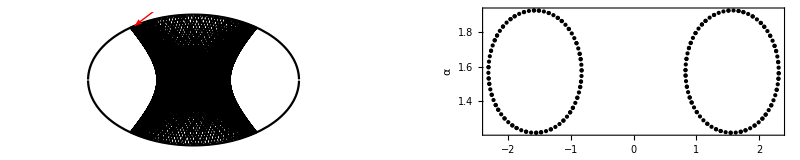

```mathematica
nextCoord[1,1.5, 2.26, 5.28-.2,0 ,200]
```

```mathematica
Pi
```

π

```mathematica
p2 = gr2;
```

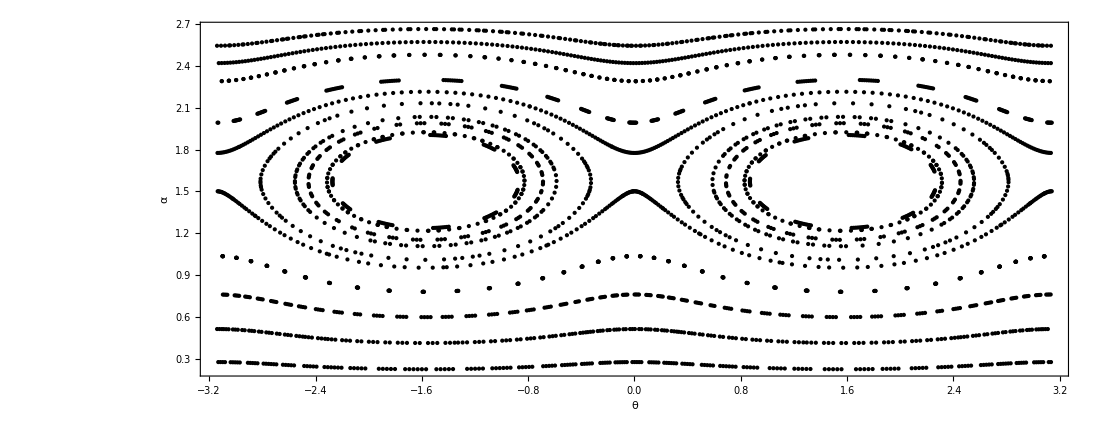

```mathematica
Show[p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13,p14,p15]
```

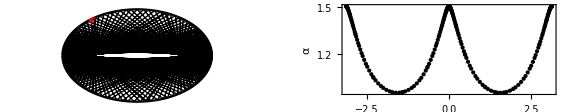

```mathematica
nextCoord[1,1.5, 2.26, 5.28-.6,0 ,200]
```

```mathematica
p3 = gr2;
```

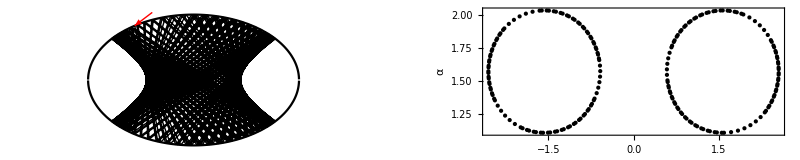

```mathematica
nextCoord[1,1.5, 2.26, 5.28-.4,0 ,200]
```

```mathematica
p4 = gr2;
```

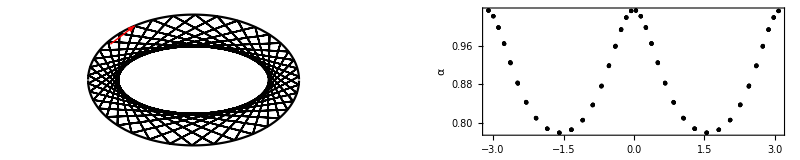

```mathematica
nextCoord[1,1.5, 2.26, 5.28-.8,0 ,200]
```

```mathematica
p5 = gr2;
```

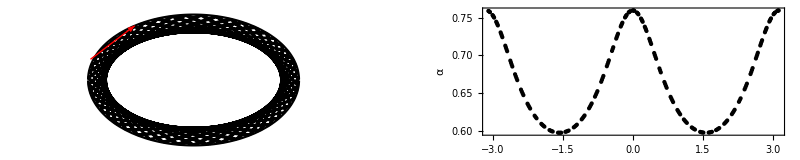

```mathematica
nextCoord[1,1.5, 2.26, 5.28-1,0 ,200]
```

```mathematica
p6 = gr2;
```

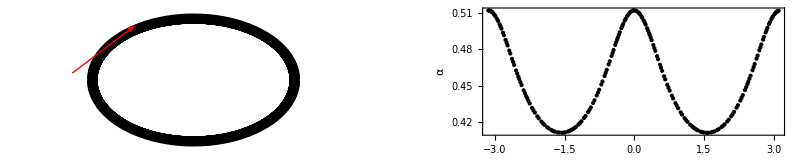

```mathematica
nextCoord[1,1.5, 2.26, 5.28-1.2,0 ,200]
```

```mathematica
p7 = gr2;
```

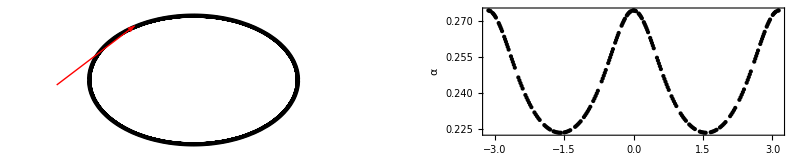

```mathematica
nextCoord[1,1.5, 2.26, 5.28-1.4,0 ,200]
```

```mathematica
p8 = gr2;
```

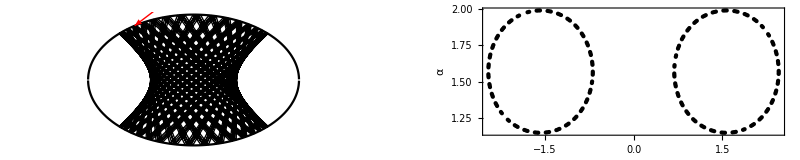

```mathematica
nextCoord[1,1.5, 2.26, 5.28+.2,0 ,200]
```

```mathematica
p9 = gr2;
```

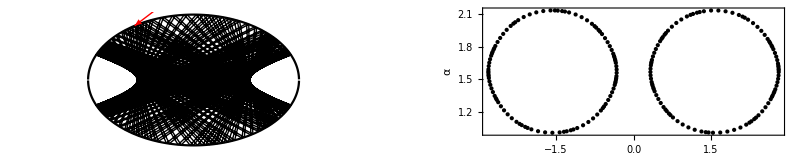

```mathematica
nextCoord[1,1.5, 2.26, 5.28+.4,0 ,200]
```

```mathematica
p10 = gr2;
```

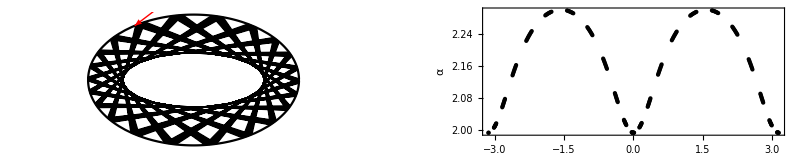

```mathematica
nextCoord[1,1.5, 2.26, 5.28+.6,0 ,200]
```

```mathematica
p11 = gr2;
```

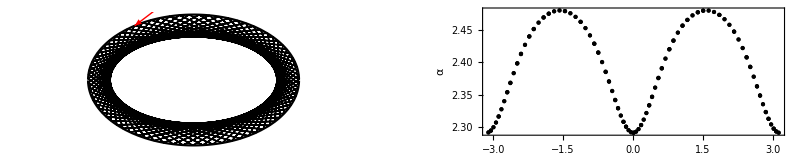

```mathematica
nextCoord[1,1.5, 2.26, 5.28+.8,0 ,200]
```

```mathematica
p12 = gr2;
```

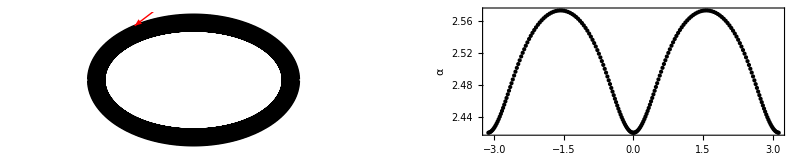

```mathematica
nextCoord[1,1.5, 2.26, 5.28+.9,0 ,200]
```

```mathematica
p13 = gr2;
```

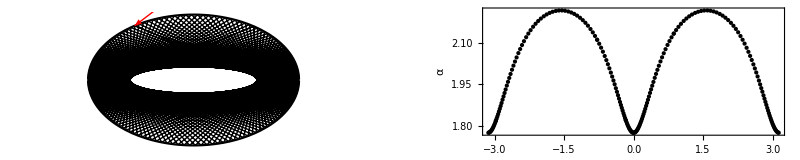

```mathematica
nextCoord[1,1.5, 2.26, 5.28+.5,0 ,200]
```

```mathematica
p14 = gr2;
```

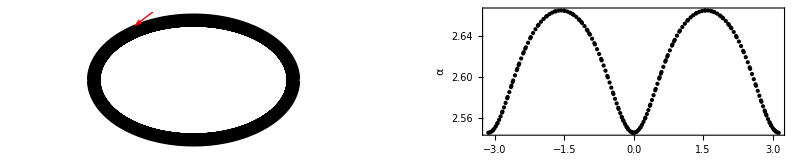

```mathematica
nextCoord[1,1.5, 2.26, 5.28+1,0 ,200]
```

```mathematica
p15 = gr2;
```

```mathematica
temp = {1,2};
```

```mathematica
temp[[1]]
```

1

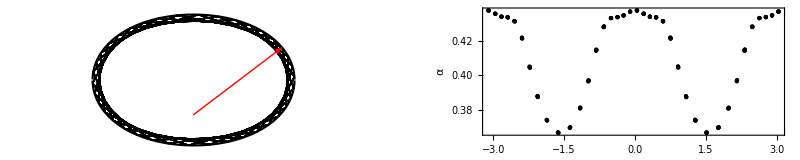

```mathematica
nextCoord[1,1.5, .45, 2.57,0.1 ,200]
```

```mathematica
q1 = gr2;
```

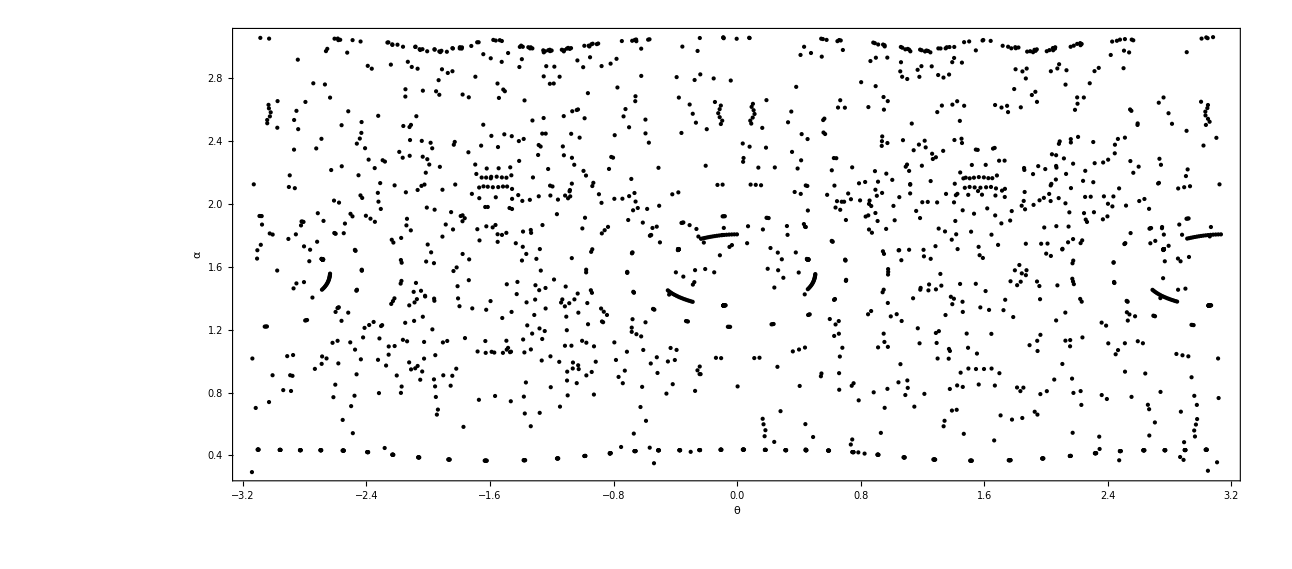

```mathematica
Show[q1,q2,q3,q4,g5,g6,g7,g8,g9,g10,g11,g12,g13,g14]
```

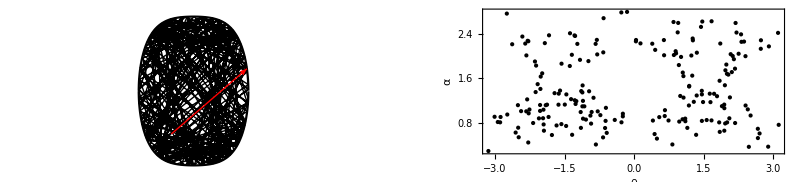

```mathematica
nextCoord[1,1.5, .45, 2.57-.2,10 ,200]
```

```mathematica
q2 = gr2;
```

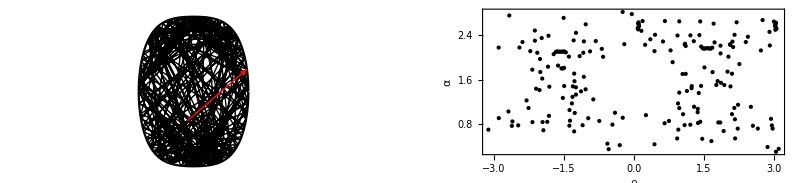

```mathematica
nextCoord[1,1.5, .45, 2.57-.4,10 ,200]
```

```mathematica
q3 = gr2;
```

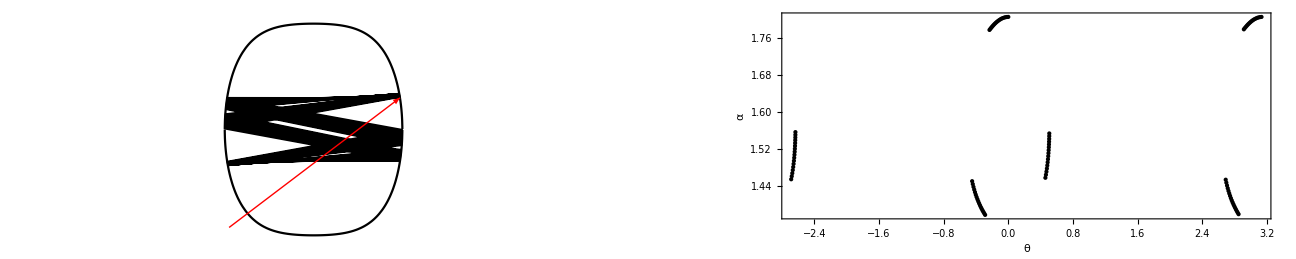

```mathematica
nextCoord[1,1.5, .45, 3.14,10 ,100]
```

```mathematica
q4 = gr2;
```

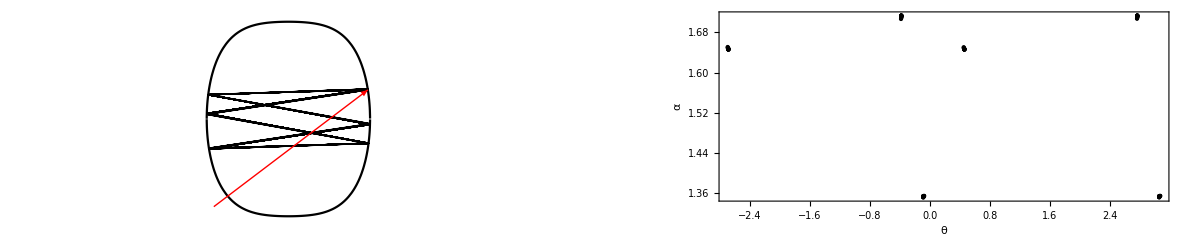

```mathematica
nextCoord[1,1.5, .45, 3.14+.2,10 ,100]
```

```mathematica
g5 = gr2;
```

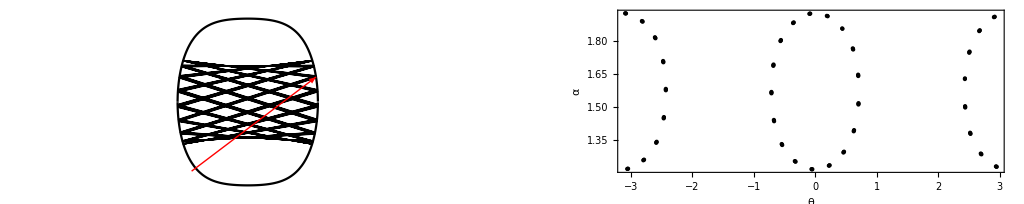

```mathematica
nextCoord[1,1.5, .45, 3.14+.4,10 ,100]
```

```mathematica
g6 = gr2;
```

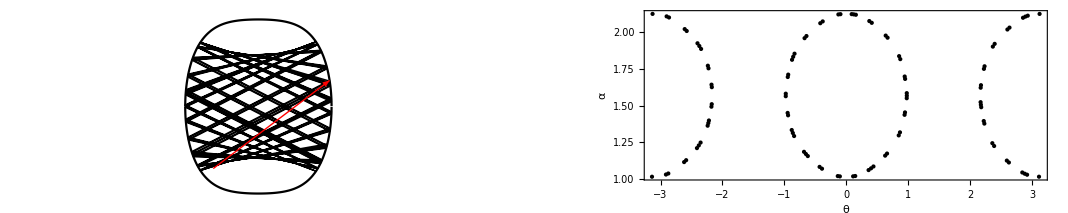

```mathematica
nextCoord[1,1.5, .45, 3.14+.6,10 ,100]
```

```mathematica
g14=gr2;
```

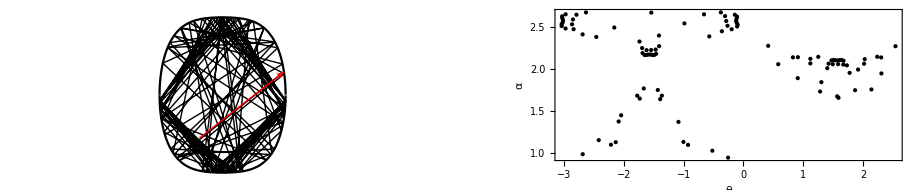

```mathematica
nextCoord[1,1.5, .45, 3.14+.8,10 ,100]
```

```mathematica
g7 = gr2;
```

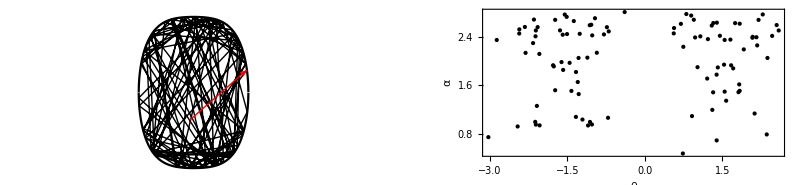

```mathematica
nextCoord[1,1.5, .45, 3.14+1,10 ,100]
```

```mathematica
g8 = gr2;
```

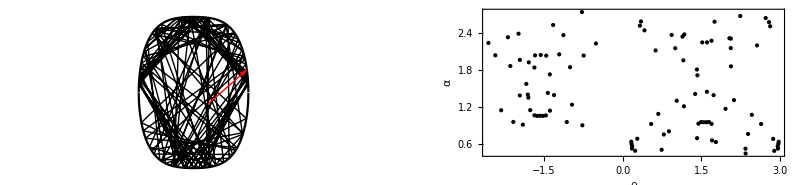

```mathematica
nextCoord[1,1.5, .45, 3.14+1.2,10 ,100]
```

```mathematica
g9 = gr2;
```

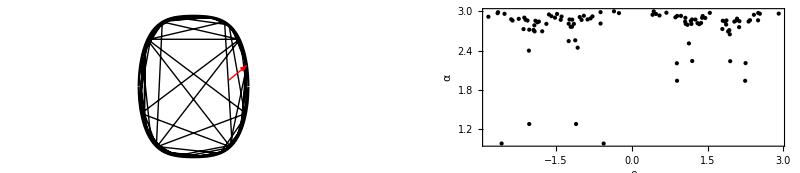

```mathematica
nextCoord[1,1.5, .45, 3.14+1.4,10 ,100]
```

```mathematica
g10 = gr2;
```

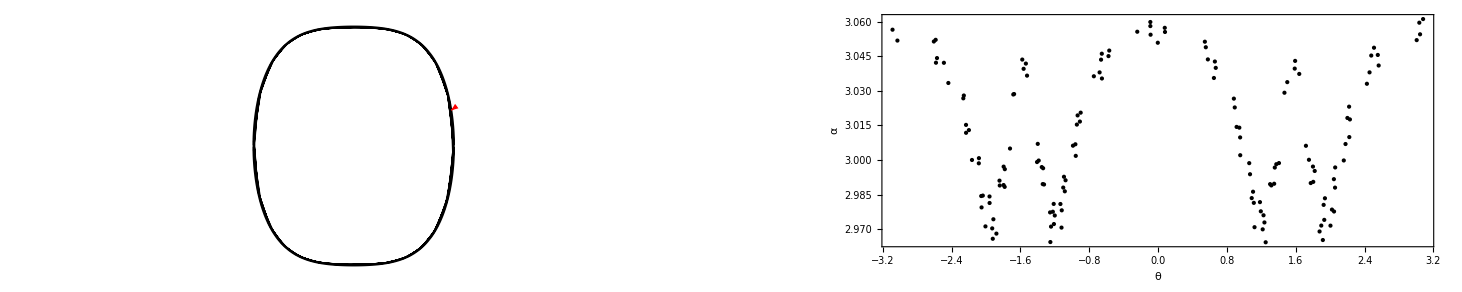

```mathematica
nextCoord[1,1.5, .45, 3.14+1.6,10 ,150]
```

```mathematica
g11 = gr2;
```

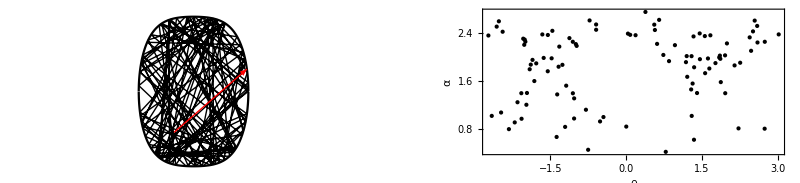

```mathematica
nextCoord[1,1.5, .45, 3.14+.81,10 ,100]
```

```mathematica
g12 = gr2;
```

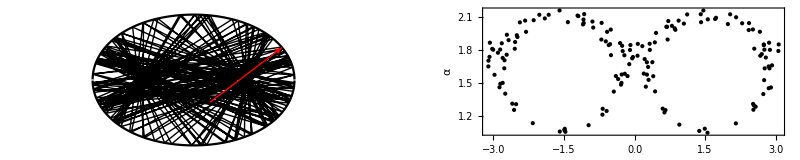

```mathematica
nextCoord[1,1.5, .45, 3.14+.82,0.1 ,150]
```

```mathematica
g13 = gr2;
```

```mathematica
nextCoord[1,1.5, .45, 3.14+2.05,0.1 ,100]
```

Part::partw: Part 2 of {0.93085} does not exist.

Part::partw: Part 2 of {-0.19738} does not exist.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::cndvs: The input to NSolve should not contain conditionally valid subexpressions.

Part::partd: Part specification NSolve[{-1+x^2+0.1 x^4+1.5 y^2==0,x==t Cos[Plus[«3»]]+If[ConditionalExpression[And[«2»],Less[«2»]],xx$1081574⟦2⟧,xx$1081574⟦1⟧],y==If[ConditionalExpression[And[«2»],Less[«2»]],yy$1081574⟦2⟧,yy$1081574⟦1⟧]+t Sin[Plus[«3»]],t≥0},{x,y,t},Reals]⟦All,1,2⟧ is longer than depth of object.

NSolve::cndvs: The input to NSolve should not contain conditionally valid subexpressions.

Part::partd: Part specification NSolve[{-1+x^2+0.1 x^4+1.5 y^2==0,x==t Cos[Plus[«3»]]+If[ConditionalExpression[And[«2»],Less[«2»]],xx$1081574⟦2⟧,xx$1081574⟦1⟧],y==If[ConditionalExpression[And[«2»],Less[«2»]],yy$1081574⟦2⟧,yy$1081574⟦1⟧]+t Sin[Plus[«3»]],t≥0},{x,y,t},Reals]⟦All,1,2⟧ is longer than depth of object.

Part::partd: Part specification NSolve[{-1+x^2+0.1 x^4+1.5 y^2==0,x==t Cos[Plus[«3»]]+If[ConditionalExpression[And[«2»],Less[«2»]],xx$1081574⟦2⟧,xx$1081574⟦1⟧],y==If[ConditionalExpression[And[«2»],Less[«2»]],yy$1081574⟦2⟧,yy$1081574⟦1⟧]+t Sin[Plus[«3»]],t≥0},{x,y,t},Reals]⟦All,2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NSolve::cndvs: The input to NSolve should not contain conditionally valid subexpressions.

General::stop: Further output of NSolve::cndvs will be suppressed during this calculation.

$Aborted

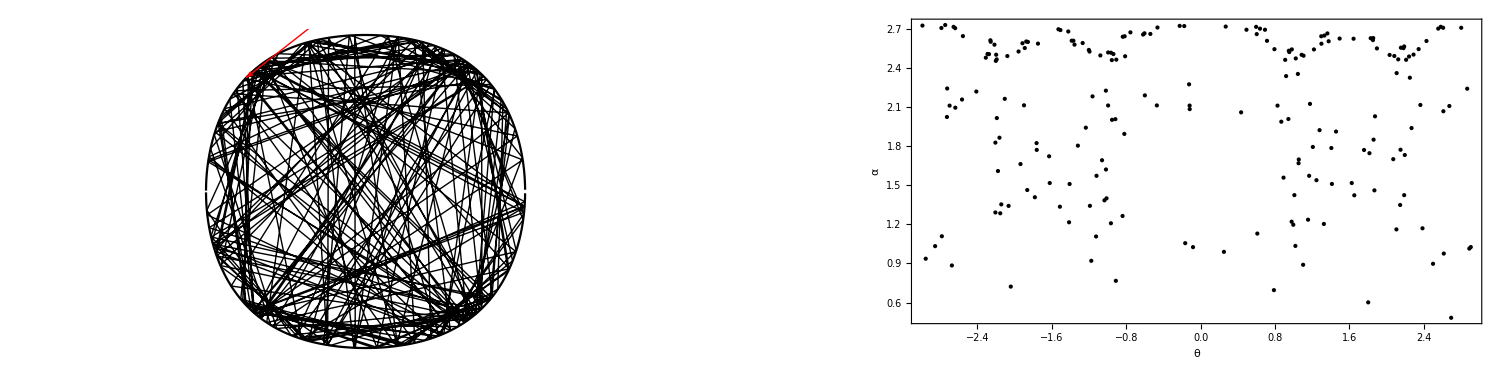

```mathematica
nextCoord[1,1, 2.26, 5.28,0 ,200]
```